```mathematica
(*Import Vacuum*)
{parameters["24.0"],ImG1["24.0"],ImGC1["24.0"],ImGL1["24.0"],ImGQ1["24.0"],ImGV1["24.0"],ImG2["24.0"],ImGC2["24.0"],ImGL2["24.0"],ImGQ2["24.0"],ImGV2["24.0"],ImG3["24.0"],ImGC3["24.0"],ImGL3["24.0"],ImGQ3["24.0"],ImGV3["24.0"],ReGC1["24.0"],ReGL1["24.0"],ReGQ1["24.0"],ReGV1["24.0"],ReGC2["24.0"],ReGL2["24.0"],ReGQ2["24.0"],ReGV2["24.0"],ReGC3["24.0"],ReGL3["24.0"],ReGQ3["24.0"],ReGV3["24.0"],C0["24.0"],Fraction["24.0"],SpatialConstInter["24.0"],SpatialTotalInter["24.0"],SpatialNon["24.0"],EuclideanConstInter["24.0"],EuclideanTotalInter["24.0"],EuclideanNon["24.0"],EuclideanExt["24.0"]}=Import["Spectralcc24.97.0.m"];
```

```mathematica
(*Import Medium*)
{parameters["24.1"],ImG1["24.1"],ImGC1["24.1"],ImGL1["24.1"],ImGQ1["24.1"],ImGV1["24.1"],ImG2["24.1"],ImGC2["24.1"],ImGL2["24.1"],ImGQ2["24.1"],ImGV2["24.1"],ImG3["24.1"],ImGC3["24.1"],ImGL3["24.1"],ImGQ3["24.1"],ImGV3["24.1"],ReGC1["24.1"],ReGL1["24.1"],ReGQ1["24.1"],ReGV1["24.1"],ReGC2["24.1"],ReGL2["24.1"],ReGQ2["24.1"],ReGV2["24.1"],ReGC3["24.1"],ReGL3["24.1"],ReGQ3["24.1"],ReGV3["24.1"],C0["24.1"],Fraction["24.1"],SpatialConstInter["24.1"],SpatialTotalInter["24.1"],SpatialNon["24.1"],EuclideanConstInter["24.1"],EuclideanTotalInter["24.1"],EuclideanNon["24.1"],EuclideanExt["24.1"]}=Import["Spectralcc24.97.1.m"];
```

```mathematica
(*conversion between i and j to s and P and exact definition of hbarc*)
i1[s_,P_]:=10Sqrt[s+P^2]
j1[s_,P_]:=10(P-Sqrt[s+P^2])
i2[s_,P_]:=936/5+Sqrt[s+P^2]
j2[s_,P_]:=10(P-Sqrt[s+P^2])
P[i_,j_]:=If[j≤150,If[i≤208,(i+j)/10,i+j/10-187.2],(4i)/5]
s[i_,j_]:=If[j≤150,If[i≤208,(-i j)/50-j^2/100,-(j/5)(i-187.2)-j^2/100],If[j≤181,((j-151)/10)^2,If[j≤381,((j-181)/100+3)^2,((j-381)/10+5)^2]]]
hbarc=6621486190496429/(10681177560000000 π);
```

```mathematica
(*Stitch the interpolation function together*)
ImG[s_,P_,version_]:=If[s<0&&P<Sqrt[s+P^2]+15,If[s+P^2≤20.8^2,ImG1[version][i1[s,P],j1[s,P]],ImG2[version][i2[s,P],j2[s,P]]],If[s≥0,ImG3[version][P,s],0]];
ImGC[s_,P_,version_]:=If[s<0&&P<Sqrt[s+P^2]+15,If[s+P^2≤20.8^2,ImGC1[version][i1[s,P],j1[s,P]],ImGC2[version][i2[s,P],j2[s,P]]],If[s≥0,ImGC3[version][P,s],0]];
ImGL[s_,P_,version_]:=If[s<0&&P<Sqrt[s+P^2]+15,If[s+P^2≤20.8^2,ImGL1[version][i1[s,P],j1[s,P]],ImGL2[version][i2[s,P],j2[s,P]]],If[s≥0,ImGL3[version][P,s],0]];
ImGQ[s_,P_,version_]:=If[s<0&&P<Sqrt[s+P^2]+15,If[s+P^2≤20.8^2,ImGQ1[version][i1[s,P],j1[s,P]],ImGQ2[version][i2[s,P],j2[s,P]]],If[s≥0,ImGQ3[version][P,s],0]];
ImGV[s_,P_,version_]:=If[s<0&&P<Sqrt[s+P^2]+15,If[s+P^2≤20.8^2,ImGV1[version][i1[s,P],j1[s,P]],ImGV2[version][i2[s,P],j2[s,P]]],If[s≥0,ImGV3[version][P,s],0]];
ReGC[s_,P_,version_]:=If[s<0&&P<Sqrt[s+P^2]+15,If[s+P^2≤20.8^2,ReGC1[version][i1[s,P],j1[s,P]],ReGC2[version][i2[s,P],j2[s,P]]],If[s≥0,ReGC3[version][P,s],0]];
ReGL[s_,P_,version_]:=If[s<0&&P<Sqrt[s+P^2]+15,If[s+P^2≤20.8^2,ReGL1[version][i1[s,P],j1[s,P]],ReGL2[version][i2[s,P],j2[s,P]]],If[s≥0,ReGL3[version][P,s],0]];
ReGQ[s_,P_,version_]:=If[s<0&&P<Sqrt[s+P^2]+15,If[s+P^2≤20.8^2,ReGQ1[version][i1[s,P],j1[s,P]],ReGQ2[version][i2[s,P],j2[s,P]]],If[s≥0,ReGQ3[version][P,s],0]];
ReGV[s_,P_,version_]:=If[s<0&&P<Sqrt[s+P^2]+15,If[s+P^2≤20.8^2,ReGV1[version][i1[s,P],j1[s,P]],ReGV2[version][i2[s,P],j2[s,P]]],If[s≥0,ReGV3[version][P,s],0]];
```

```mathematica
(*Spectral functions*)
σNon[s_,P_,version_]:=-3/π ImG[s,P,version]
σC[s_,P_,version_]:=3/π C0[version] Fraction[version] Im[(1/4(ReGC[s,P,version]+ⅈ ImGC[s,P,version])^2)/(1-(ReGV[s,P,version]+ⅈ ImGV[s,P,version]))]
σL[s_,P_,version_]:=3/π C0[version] Fraction[version] Im[(ReGL[s,P,version]+ⅈ ImGL[s,P,version])^2/(1-(ReGV[s,P,version]+ⅈ ImGV[s,P,version]))]
σQ[s_,P_,version_]:=3/π C0[version] Fraction[version]Im[(ReGQ[s,P,version]+ⅈ ImGQ[s,P,version])^2/(1-(ReGV[s,P,version]+ⅈ ImGV[s,P,version]))]
σConstInter[s_,P_,version_]:=8σC[s,P,version]
σTotalInter[s_,P_,version_]:=σC[s,P,version]+σL[s,P,version]+σQ[s,P,version]
σConst[s_,P_,version_]:=σNon[s,P,version]+σConstInter[s,P,version]
σTotal[s_,P_,version_]:=σNon[s,P,version]+σTotalInter[s,P,version]
```

```mathematica
(*On-shell Potential*)
V["24"][s_,P_,T_,version_]:=C0[version]/(4π)Fraction[version] ((2 2.29444^2)/(2 2.29444^2+(parameters[version][[2]] T)^2+Ramp[s-4(parameters[version][[3]])^2]))^4
```

```mathematica
(*T-Matrix*)
ImT[s_,P_,T_,version_]:=V[StringTake[version,2]][s,P,T,version]Im[1/(1-(ReGV[s,P,version]+ⅈ ImGV[s,P,version]))]
ReT[s_,P_,T_,version_]:=V[StringTake[version,2]][s,P,T,version]Re[1/(1-(ReGV[s,P,version]+ⅈ ImGV[s,P,version]))]
```

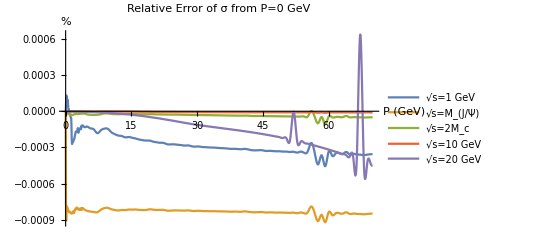

```mathematica
(*Relative error of the spectral function at select s in vacuum*)
Plot[{100(σTotal[1,P,"24.0"]/σTotal[1,0,"24.0"]-1),100(σTotal[3.0402476995009065^2,P,"24.0"]/σTotal[3.0402476995009065^2,0,"24.0"]-1),100(σTotal[12.96,P,"24.0"]/σTotal[12.96,0,"24.0"]-1),100(σTotal[100,P,"24.0"]/σTotal[100,0,"24.0"]-1),100(σTotal[400,P,"24.0"]/σTotal[400,0,"24.0"]-1)},{P,0,70},PlotLabel->"Relative Error of σ from P=0 GeV",PlotLegends->{"√s=1 GeV","√s=M_(J/Ψ)","√s=2M_c","√s=10 GeV","√s=20 GeV"},AxesLabel->{"P (GeV)","%"},AxesStyle->Black,LabelStyle->Black]
```

```mathematica
(*Colors to hide non-automatic color choices*)
Color={RGBColor[0.368417,0.506779,0.709798],RGBColor[0.880722,0.611041,0.142051],RGBColor[0.560181,0.691569,0.194885],RGBColor[0.922526,0.385626,0.209179],RGBColor[0.528488,0.470624,0.701351]}
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351]}

```mathematica
(*Scub through P*)
Manipulate[{Plot[{σConst[x^2,P,"24.0"],σConst[x^2,P,"24.1"]},{x,2,4.5},PlotRange->{0,5},ImageSize->Medium,PlotLabel->"V=10b Constant Trace",PlotStyle->Join[{Black},Color]],Plot[{σTotal[x^2,P,"24.0"],σTotal[x^2,P,"24.1"]},{x,2,4.5},PlotRange->{0,5},ImageSize->Medium,PlotLabel->"V=10b Full Trace",PlotStyle->Join[{Black},Color]]},{P,0,32}]
```

```mathematica
LaunchKernels[12]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
ParallelEvaluate[Off[FindMaximum::lstol]]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
(*Find the peak*)
MJΨ["24.0"]=Interpolation[ParallelTable[{P,FindMaximum[{σTotalInter[x^2,P,"24.0"],x>2&&x<5},{x,3.0404}][[2,1,2]]},{P,0,100,.8}]];
MJΨ["24.1"]=Interpolation[ParallelTable[{P,FindMaximum[{σTotalInter[x^2,P,"24.1"],x>2&&x<5},{x,3.0404}][[2,1,2]]},{P,0,70.4,.8}]];
```

```mathematica
(*Measure its width*)
Γ["24.0"]=Interpolation[Table[{P,(4√(-10^-10 σTotalInter[(MJΨ["24.0"][P])^2,P,"24.0"]/(2(σTotalInter[(MJΨ["24.0"][P]-10^-5)^2,P,"24.0"]-2 σTotalInter[(MJΨ["24.0"][P])^2,P,"24.0"]+σTotalInter[(MJΨ["24.0"][P]+10^-5)^2,P,"24.0"]))))},{P,0,100,.8}]];
Γ["24.1"]=Interpolation[Table[{P,(4√(-10^-10 σTotalInter[(MJΨ["24.1"][P])^2,P,"24.1"]/(2(σTotalInter[(MJΨ["24.1"][P]-10^-5)^2,P,"24.1"]-2 σTotalInter[(MJΨ["24.1"][P])^2,P,"24.1"]+σTotalInter[(MJΨ["24.1"][P]+10^-5)^2,P,"24.1"]))))},{P,0,70.4,.8}]];
```

```mathematica
(*Measure its width another way*)
ΓD["24.0"]=Interpolation[Table[{P,FindRoot[σTotalInter[x^2,P,"24.0"]==σTotalInter[(MJΨ["24.0"][P])^2,P,"24.0"]/2,{x,MJΨ["24.0"][P]+.1}][[1,2]]-FindRoot[σTotalInter[x^2,P,"24.0"]==σTotalInter[(MJΨ["24.0"][P])^2,P,"24.0"]/2,{x,MJΨ["24.0"][P]-.1}][[1,2]]},{P,0,100,.8}]];
ΓD["24.1"]=Interpolation[Table[{P,FindRoot[σTotalInter[x^2,P,"24.1"]==σTotalInter[(MJΨ["24.1"][P])^2,P,"24.1"]/2,{x,MJΨ["24.1"][P]+.2}][[1,2]]-FindRoot[σTotalInter[x^2,P,"24.1"]==σTotalInter[(MJΨ["24.1"][P])^2,P,"24.1"]/2,{x,MJΨ["24.1"][P]-.2}][[1,2]]},{P,0,70.4,.8}]];
```

```mathematica
(*Measure its area one way*)
Amp["24.0"]=Interpolation[Table[{P,π σTotalInter[(MJΨ["24.0"][P])^2,P,"24.0"]Γ["24.0"][P]/2},{P,0,100,.8}]];
Amp["24.1"]=Interpolation[Table[{P,π σTotalInter[(MJΨ["24.1"][P])^2,P,"24.1"]Γ["24.1"][P]/2},{P,0,70.4,.8}]];
```

```mathematica
(*Measure its area another way*)
F["24.0"]=Interpolation[ParallelTable[{P,NIntegrate[σTotalInter[x^2,P,"24.0"],{x,2,4}]},{P,0,100,.8}]];
F["24.1"]=Interpolation[ParallelTable[{P,NIntegrate[σTotalInter[x^2,P,"24.1"],{x,2,5}]},{P,0,70.4,.8}]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.27144}. NIntegrate obtained -0.683465 and 0.180932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.27144}. NIntegrate obtained -0.644016 and 2.7693×10^-6 for the integral and error estimates.

```mathematica
CloseKernels[]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
(*Binding Energy definition*)
Ebind[P_,version_]:=2parameters[version][[3]]-MJΨ[version][P]
```

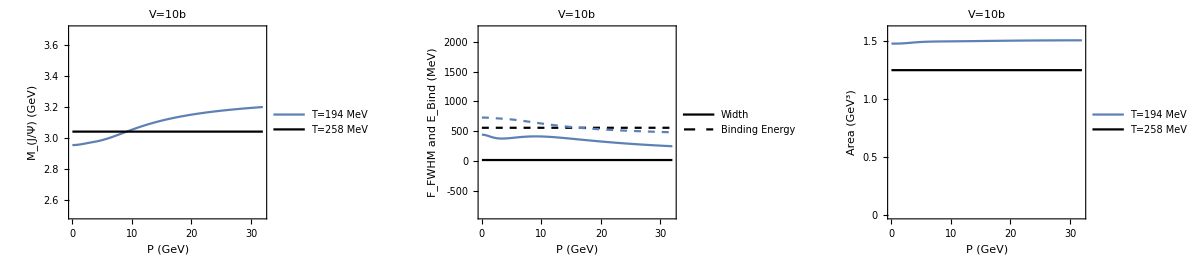

```mathematica
(*Plot of spectral function characteristics*)
GraphicsGrid[{{Plot[{MJΨ["24.1"][P],MJΨ["24.0"][P]},{P,0,32},PlotStyle->{Automatic,Black},LabelStyle->Black,PlotRange->{2.5,3.7},PlotLegends->Placed[LineLegend[{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","Vacuum"},LegendLayout->{"Row",2}],{0.5,0.25}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"P (GeV)","M_(J/Ψ) (GeV)"},FrameTicks->All,FrameStyle->Black,PlotLabel->"V=10b"],Plot[{Γ["24.0"][P]1000,Ebind[P,"24.0"]1000,Γ["24.1"][P]1000,Ebind[P,"24.1"]1000},{P,0,32},PlotStyle->{Black,{Black,Dashed},Color[[1]],{Dashed,Color[[1]]}},PlotRange->{-900,2200},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"Width","Binding Energy"},LegendLayout->{"Row",1}],{0.5,0.75}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"P (GeV)","F_FWHM and E_Bind (MeV)"},FrameTicks->All,FrameStyle->Black,PlotLabel->"V=10b"],Plot[{F["24.1"][P],F["24.0"][P]},{P,0,32},PlotStyle->{Automatic,Black},LabelStyle->Black,PlotRange->{0,1.6},PlotLegends->Placed[LineLegend[{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","Vacuum"},LegendLayout->{"Row",2}],{0.5,0.25}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"P (GeV)","Area (GeV^3)"},FrameTicks->All,FrameStyle->Black,PlotLabel->"V=10b"]}},ImageSize->1200]
```

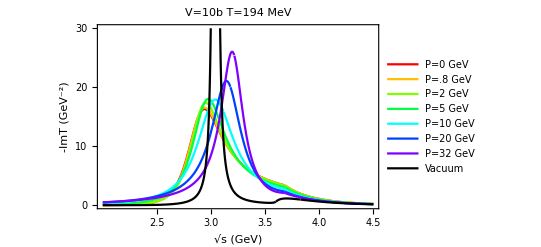

```mathematica
(*Plot P-dependence of -ImT-matrix*)
Plot[{ImT[x^2,0,.194,"24.1"],ImT[x^2,.8,.194,"24.1"],ImT[x^2,2,.194,"24.1"],ImT[x^2,5,.194,"24.1"],ImT[x^2,10,.194,"24.1"],ImT[x^2,20,.194,"24.1"],ImT[x^2,32,.194,"24.1"],ImT[x^2,0,0,"24.0"]},{x,2,4.5},PlotRange->{0,30},PlotLabel->"V=10b T=194 MeV",PlotStyle->Join[Table[Hue[i/8],{i,0,6}],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"P=0 GeV","P=.8 GeV","P=2 GeV","P=5 GeV","P=10 GeV","P=20 GeV","P=32 GeV","Vacuum"}],{0.18,0.5}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","-ImT (GeV^-2)"},FrameTicks->All,FrameStyle->Black]
```

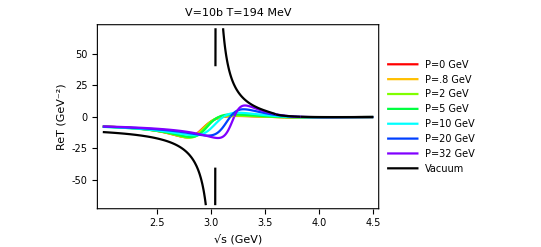

```mathematica
(*Plot P-dependence of ReT-matrix*)
Plot[{-ReT[x^2,0,.194,"24.1"],-ReT[x^2,.8,.194,"24.1"],-ReT[x^2,2,.194,"24.1"],-ReT[x^2,5,.194,"24.1"],-ReT[x^2,10,.194,"24.1"],-ReT[x^2,20,.194,"24.1"],-ReT[x^2,32,.194,"24.1"],-ReT[x^2,0,0,"24.0"]},{x,2,4.5},PlotRange->{-70,70},PlotLabel->"V=10b T=194 MeV",PlotStyle->Join[Table[Hue[i/8],{i,0,6}],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"P=0 GeV","P=.8 GeV","P=2 GeV","P=5 GeV","P=10 GeV","P=20 GeV","P=32 GeV","Vacuum"}],{0.18,0.5}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","ReT (GeV^-2)"},FrameTicks->All,FrameStyle->Black]
```

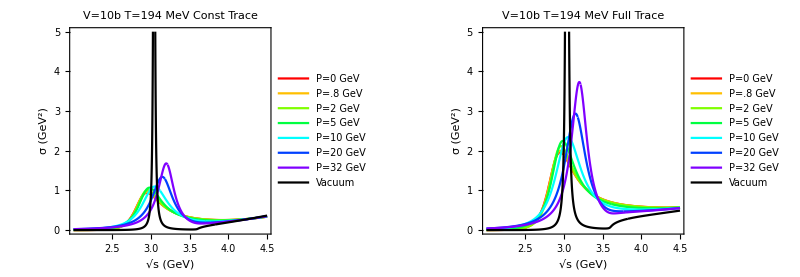

```mathematica
(*Plot P-dependence of Spectral function on log scale*)
GraphicsGrid[{{Plot[{σConst[x^2,0,"24.1"],σConst[x^2,.8,"24.1"],σConst[x^2,2,"24.1"],σConst[x^2,5,"24.1"],σConst[x^2,10,"24.1"],σConst[x^2,20,"24.1"],σConst[x^2,32,"24.1"],σConst[x^2,0,"24.0"]},{x,2,4.5},PlotRange->{0,5},PlotLabel->"V=10b T=194 MeV Const Trace",PlotStyle->Join[Table[Hue[i/8],{i,0,6}],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"P=0 GeV","P=.8 GeV","P=2 GeV","P=5 GeV","P=10 GeV","P=20 GeV","P=32 GeV","Vacuum"}],{0.18,0.5}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","σ (GeV^2)"},FrameTicks->All,FrameStyle->Black],Plot[{σTotal[x^2,0,"24.1"],σTotal[x^2,.8,"24.1"],σTotal[x^2,2,"24.1"],σTotal[x^2,5,"24.1"],σTotal[x^2,10,"24.1"],σTotal[x^2,20,"24.1"],σTotal[x^2,32,"24.1"],σTotal[x^2,0,"24.0"]},{x,2,4.5},PlotRange->{0,5},PlotLabel->"V=10b T=194 MeV Full Trace",PlotStyle->Join[Table[Hue[i/8],{i,0,6}],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"P=0 GeV","P=.8 GeV","P=2 GeV","P=5 GeV","P=10 GeV","P=20 GeV","P=32 GeV","Vacuum"}],{0.18,0.5}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","σ (GeV^2)"},FrameTicks->All,FrameStyle->Black]}},ImageSize->800]
```

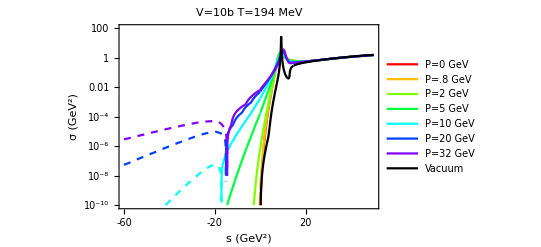

```mathematica
(*Plot P-dependence of spectral function on logscale*)
Off[Less::nord,Min::nord,Max::nord,GreaterEqual::nord];
LogPlot[{σTotal[s,0,"24.1"],σTotal[s,.8,"24.1"],σTotal[s,2,"24.1"],σTotal[s,5,"24.1"],σTotal[s,10,"24.1"],σTotal[s,20,"24.1"],σTotal[s,32,"24.1"],σTotal[s,0,"24.0"],-σTotal[s,0,"24.1"],-σTotal[s,.8,"24.1"],-σTotal[s,2,"24.1"],-σTotal[s,5,"24.1"],-σTotal[s,10,"24.1"],-σTotal[s,20,"24.1"],-σTotal[s,32,"24.1"]},{s,-60,50},PlotStyle->Join[Table[Hue[i/8],{i,0,6}],{Black},Table[{Dashed,Hue[i/8]},{i,0,6}]],PlotLegends->{Placed[LineLegend[{"P=0 GeV","P=.8 GeV","P=2 GeV"}],{0.25,0.8}],Placed[LineLegend[{None,None,None,"P=5 GeV","P=10 GeV","P=20 GeV","P=32 GeV","Vacuum"}],{0.8,0.35}]},PlotLabel->"V=10b T=194 MeV",LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"s (GeV^2)","σ (GeV^2)"},FrameTicks->All,FrameStyle->Black,PlotRange->{10^-10,100}]
```

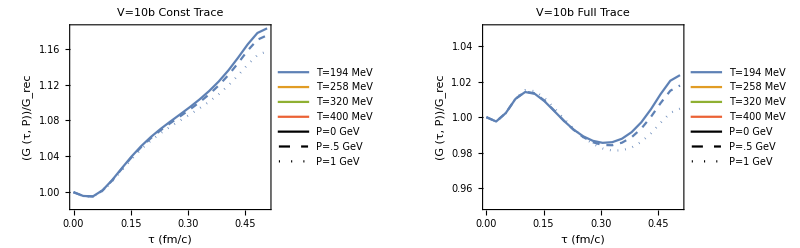

```mathematica
(*Plot P-dependence of Euclidean correlation ratio versus vacuum at the same P*)
GraphicsGrid[{{ListPlot[Flatten[{Table[{EuclideanConstInter["24.1"][[i,j,1]] hbarc/(.194),(Total[EuclideanConstInter["24.1"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[i,j,3,1]])/(Total[EuclideanConstInter["24.0"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.0"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.0"][[i,j,3,1]])},{i,3},{j,21}]},1],Joined->True,PlotLabel->"V=10b Const Trace",PlotStyle->Flatten[Table[{Color[[i]],{Automatic,Dashed,Dotted}[[j]]},{i,5},{j,3}],1],LabelStyle->Black,PlotLegends->Placed[LineLegend[Join[Color[[;;4]],{Black,{Black,Dashed},{Black,Dotted}}],{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","P=0 GeV","P=.5 GeV","P=1 GeV"},LegendLayout->{"Column",2},LegendMarkerSize->10],{0.75,0.25}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black],ListPlot[Flatten[{Table[{EuclideanTotalInter["24.1"][[i,j,1]] hbarc/(.194),(Total[EuclideanTotalInter["24.1"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[i,j,3,1]])/(Total[EuclideanTotalInter["24.0"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.0"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.0"][[i,j,3,1]])},{i,3},{j,21}]},1],Joined->True,PlotLabel->"V=10b Full Trace",PlotStyle->Flatten[Table[{Color[[i]],{Automatic,Dashed,Dotted}[[j]]},{i,5},{j,3}],1],LabelStyle->Black,PlotLegends->Placed[LineLegend[Join[Color[[;;4]],{Black,{Black,Dashed},{Black,Dotted}}],{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","P=0 GeV","P=.5 GeV","P=1 GeV"},LegendLayout->{"Column",2},LegendMarkerSize->10],{0.75,0.25}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black,PlotRange->{.95,1.05}]}},ImageSize->800]
```

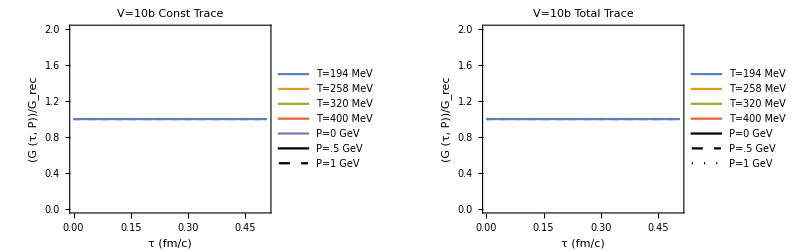

```mathematica
(*Plot P-dependence of Euclidean correlation ratio versus coldest T above vacuum*)
GraphicsGrid[{{ListPlot[Flatten[{Table[{EuclideanConstInter["24.1"][[i,j,1]] hbarc/(.194),(Total[EuclideanConstInter["24.1"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[i,j,3,1]])/(Total[EuclideanConstInter["24.1"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[i,j,3,1]])},{i,3},{j,21}]},1],Joined->True,PlotLabel->"V=10b Const Trace",PlotStyle->Flatten[Table[{Color[[i]],{Automatic,Dashed,Dotted}[[j]]},{i,4},{j,3}],1],LabelStyle->Black,PlotLegends->Placed[LineLegend[Join[Color,{Black,{Black,Dashed},{Black,Dotted}}],{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","P=0 GeV","P=.5 GeV","P=1 GeV"},LegendLayout->{"Column",2},LegendMarkerSize->10],{0.75,0.25}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black],ListPlot[Flatten[{Table[{EuclideanTotalInter["24.1"][[i,j,1]] hbarc/(.194),(Total[EuclideanTotalInter["24.1"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[i,j,3,1]])/(Total[EuclideanTotalInter["24.1"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[i,j,3,1]])},{i,3},{j,21}]},1],Joined->True,PlotLabel->"V=10b Total Trace",LabelStyle->Black,PlotStyle->Flatten[Table[{Color[[i]],{Automatic,Dashed,Dotted}[[j]]},{i,4},{j,3}],1],LabelStyle->Black,PlotLegends->{Placed[LineLegend[Color,{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV"},LegendMarkerSize->10],{0.15,0.25}],Placed[LineLegend[{Black,{Black,Dashed},{Black,Dotted}},{"P=0 GeV","P=.5 GeV","P=1 GeV"},LegendMarkerSize->10],{0.85,0.75}]},ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black]}},ImageSize->800]
```

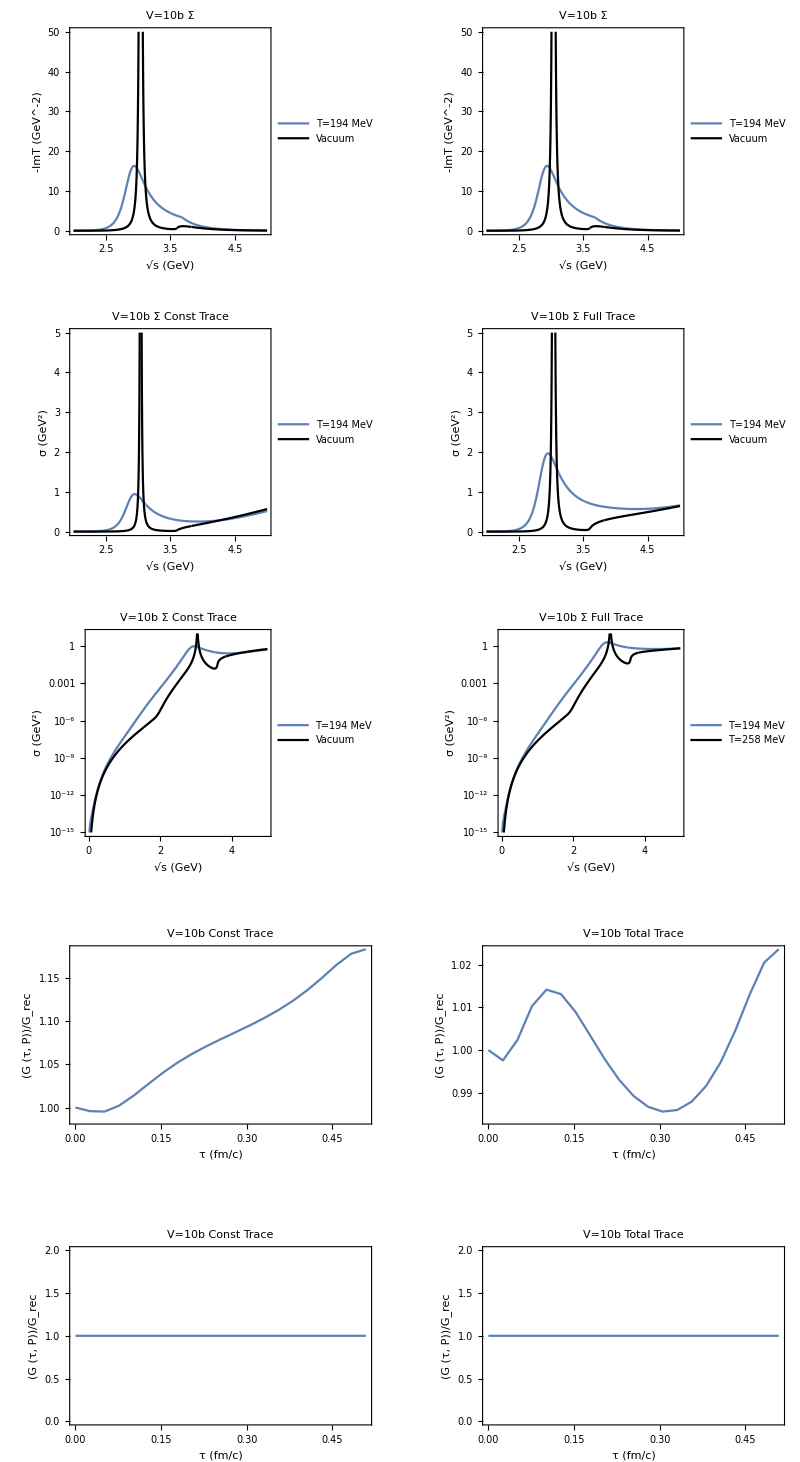

```mathematica
(*Collection of P=0 plots*)
GraphicsGrid[{{Plot[{ImT[x^2,0,.194,"24.1"],ImT[x^2,0,0,"24.0"]},{x,2,5},PlotStyle->Join[Color[[;;1]],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","Vacuum"}],{0.75,0.75}],ImageSize->400,Axes->False,PlotRange->{0,50},Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","-ImT (GeV^-2)"},FrameTicks->All,FrameStyle->Black,PlotLabel->"V=10b Σ"],Plot[{ImT[x^2,0,.194,"24.1"],ImT[x^2,0,0,"24.0"]},{x,2,5},PlotStyle->Join[Color[[;;1]],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","Vacuum"}],{0.75,0.75}],ImageSize->400,Axes->False,PlotRange->{0,50},Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","-ImT (GeV^-2)"},FrameTicks->All,FrameStyle->Black,PlotLabel->"V=10b Σ"]},{Plot[{σConst[x^2,0,"24.1"],σConst[x^2,0,"24.0"]},{x,2,5},PlotStyle->Join[Color[[;;1]],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","Vacuum"}],{0.75,0.75}],ImageSize->400,Axes->False,PlotRange->{0,5},Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","σ (GeV^2)"},FrameTicks->All,FrameStyle->Black,PlotLabel->"V=10b Σ Const Trace"],Plot[{σTotal[x^2,0,"24.1"],σTotal[x^2,0,"24.0"]},{x,2,5},PlotStyle->Join[Color[[;;1]],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","Vacuum"}],{0.75,0.75}],ImageSize->400,Axes->False,PlotRange->{0,5},Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","σ (GeV^2)"},FrameTicks->All,FrameStyle->Black,PlotLabel->"V=10b Σ Full Trace"]},{LogPlot[{σConst[x^2,0,"24.1"],σConst[x^2,0,"24.0"]},{x,0,5},PlotStyle->Join[Color[[;;1]],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","Vacuum"}],{0.75,0.35}],ImageSize->400,Axes->False,PlotRange->{10^-15,10},Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","σ (GeV^2)"},FrameTicks->All,FrameStyle->Black,PlotLabel->"V=10b Σ Const Trace"],LogPlot[{σTotal[x^2,0,"24.1"],σTotal[x^2,0,"24.0"]},{x,0,5},PlotStyle->Join[Color[[;;1]],{Black}],LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","Vacuum"}],{0.75,0.35}],ImageSize->400,Axes->False,PlotRange->{10^-15,10},Frame->{{True,False},{True,False}},FrameLabel->{"√s (GeV)","σ (GeV^2)"},FrameTicks->All,FrameStyle->Black,PlotLabel->"V=10b Σ Full Trace"]},{ListPlot[{Table[{EuclideanConstInter["24.1"][[1,j,1]] hbarc/.194,(Total[EuclideanConstInter["24.1"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[1,j,3,1]])/(Total[EuclideanConstInter["24.0"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.0"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.0"][[1,j,3,1]])},{j,21}]},Joined->True,PlotLabel->"V=10b Const Trace",LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black],ListPlot[{Table[{EuclideanTotalInter["24.1"][[1,j,1]] hbarc/.194,(Total[EuclideanTotalInter["24.1"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[1,j,3,1]])/(Total[EuclideanTotalInter["24.0"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.0"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.0"][[1,j,3,1]])},{j,21}]},Joined->True,PlotLabel->"V=10b Total Trace",LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black]},{ListPlot[{Table[{EuclideanConstInter["24.1"][[1,j,1]] hbarc/.194,(Total[EuclideanConstInter["24.1"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[1,j,3,1]])/(Total[EuclideanConstInter["24.1"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[1,j,3,1]])},{j,21}]},Joined->True,PlotLabel->"V=10b Const Trace",LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black],ListPlot[{Table[{EuclideanTotalInter["24.1"][[1,j,1]] hbarc/.194,(Total[EuclideanTotalInter["24.1"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[1,j,3,1]])/(Total[EuclideanTotalInter["24.1"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[1,j,3,1]])},{j,21}]},Joined->True,PlotLabel->"V=10b Total Trace",LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black]}},ImageSize->800]
```

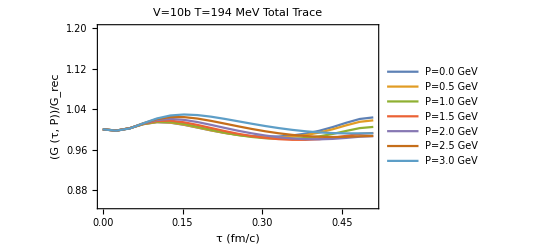

```mathematica
(*Plot P-dependence of Euclidean correlation ratio versus vacuum at the same P*)
ListPlot[Table[{EuclideanTotalInter["24.1"][[1,j,1]] hbarc/(.194),(Total[EuclideanTotalInter["24.1"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[i,j,3,1]])/(Total[EuclideanTotalInter["24.0"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.0"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.0"][[i,j,3,1]])},{i,7},{j,21}],Joined->True,PlotLabel->"V=10b T=194 MeV Total Trace",LabelStyle->Black,PlotRange->{.85,1.2},PlotLegends->Placed[LineLegend[Array["P="<>ToString[NumberForm[(#-1)/2.,{2,1}]]<>" GeV"&,7],LegendLayout->{"Column",3}],{0.5,0.8}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black]
```

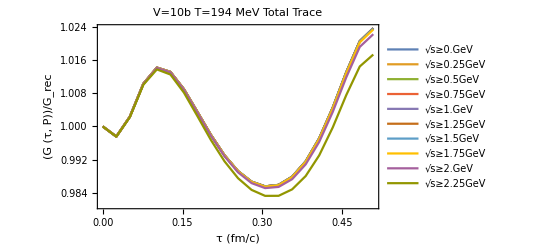

```mathematica
(*Plot √s cutoff-dependence of Euclidean correlation ratio*)
ListPlot[Table[{EuclideanTotalInter["24.1"][[1,j,1]] hbarc/(.194),(Total[EuclideanTotalInter["24.1"][[1,j,3,i;;15,2,1]]]+Total[EuclideanNon["24.1"][[1,j,3,i;;15,2,1]]]+EuclideanExt["24.1"][[1,j,3,1]])/(Total[EuclideanTotalInter["24.0"][[1,j,3,i;;15,2,1]]]+Total[EuclideanNon["24.0"][[1,j,3,i;;15,2,1]]]+EuclideanExt["24.0"][[1,j,3,1]])},{i,10},{j,21}],Joined->True,PlotLabel->"V=10b T=194 MeV Total Trace",PlotRange->Automatic,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/G_rec"},FrameTicks->All,FrameStyle->Black,LabelStyle->Black,ImageSize->Medium,PlotLegends->Table["√s≥"<>ToString[i/4.]<>"GeV",{i,0,9}]]
```

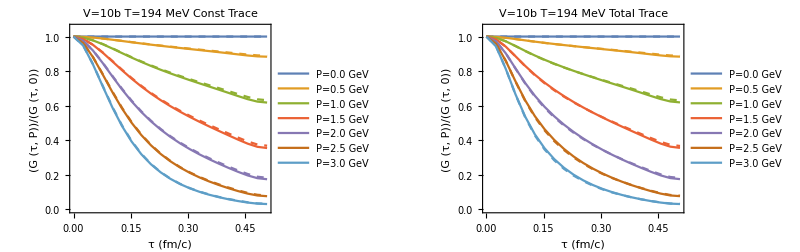

```mathematica
(*Plot P-dependence of Euclidean correlation ratio versus own T and P=0*)
GraphicsGrid[{{Show[ListPlot[Table[{EuclideanConstInter["24.0"][[i,j,1]] hbarc/.194,(Total[EuclideanConstInter["24.0"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.0"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.0"][[i,j,3,1]])/(Total[EuclideanConstInter["24.0"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.0"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.0"][[1,j,3,1]])},{i,7},{j,21}],Joined->True,PlotLabel->"V=10b T=194 MeV Const Trace",LabelStyle->Black,PlotStyle->Dashed,LabelStyle->Black,PlotRange->{0,1.05},ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/(G (τ, 0))"},FrameTicks->All,FrameStyle->Black],ListPlot[Table[{EuclideanConstInter["24.1"][[i,j,1]] hbarc/.194,(Total[EuclideanConstInter["24.1"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[i,j,3,1]])/(Total[EuclideanConstInter["24.1"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[1,j,3,1]])},{i,7},{j,21}],Joined->True,LabelStyle->Black,PlotLegends->Placed[LineLegend[Array["P="<>ToString[NumberForm[(#-1)/2.,{2,1}]]<>" GeV"&,7],LegendLayout->{"Column",1},LegendMarkerSize->10],{0.12,0.35}]],ImageSize->400],Show[ListPlot[Table[{EuclideanTotalInter["24.0"][[i,j,1]] hbarc/.194,(Total[EuclideanTotalInter["24.0"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.0"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.0"][[i,j,3,1]])/(Total[EuclideanTotalInter["24.0"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.0"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.0"][[1,j,3,1]])},{i,7},{j,21}],Joined->True,PlotLabel->"V=10b T=194 MeV Total Trace",LabelStyle->Black,PlotStyle->Dashed,LabelStyle->Black,PlotRange->{0,1.05},ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"τ (fm/c)","(G (τ, P))/(G (τ, 0))"},FrameTicks->All,FrameStyle->Black],ListPlot[Table[{EuclideanTotalInter["24.1"][[i,j,1]] hbarc/.194,(Total[EuclideanTotalInter["24.1"][[i,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[i,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[i,j,3,1]])/(Total[EuclideanTotalInter["24.1"][[1,j,3,;;15,2,1]]]+Total[EuclideanNon["24.1"][[1,j,3,;;15,2,1]]]+EuclideanExt["24.1"][[1,j,3,1]])},{i,7},{j,21}],Joined->True,LabelStyle->Black,PlotLegends->Placed[LineLegend[Array["P="<>ToString[NumberForm[(#-1)/2.,{2,1}]]<>" GeV"&,7],LegendLayout->{"Column",1},LegendMarkerSize->10],{0.12,0.35}]],ImageSize->400]}},ImageSize->800]
```

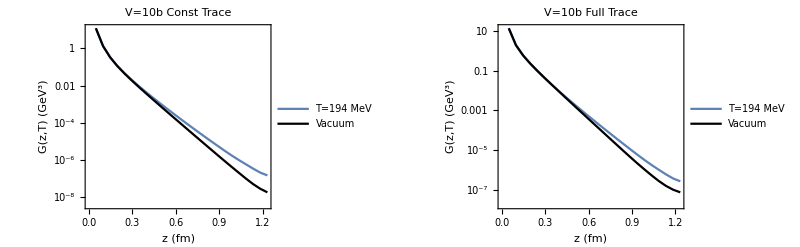

```mathematica
(*Plot of spatial correlation function*)
GraphicsGrid[{{ListLogPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,Total[SpatialConstInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]]},{i,25}],Table[{SpatialNon["24.0"][[i,1,1]]hbarc,Total[SpatialConstInter["24.0"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.0"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]]},{i,25}]},Joined->True,PlotLabel->"V=10b Const Trace",PlotStyle->{Automatic,Black},AxesLabel->{"z (fm)","G(z,T) (GeV^3)"},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","Vacuum"}],{0.8,0.7}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"z (fm)","G(z,T) (GeV^3)"},FrameTicks->{Automatic,10.^Range[-8,1]},FrameStyle->Black],ListLogPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,Total[SpatialTotalInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]]},{i,25}],Table[{SpatialNon["24.0"][[i,1,1]]hbarc,Total[SpatialTotalInter["24.0"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]]},{i,25}]},Joined->True,PlotLabel->"V=10b Full Trace",PlotStyle->{Automatic,Black},AxesLabel->{"z (fm)","G(z,T) (GeV^3)"},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","Vacuum"}],{0.8,0.7}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"z (fm)","G(z,T) (GeV^3)"},FrameTicks->{Automatic,10.^Range[-8,1]},FrameStyle->Black]}},ImageSize->800]
```

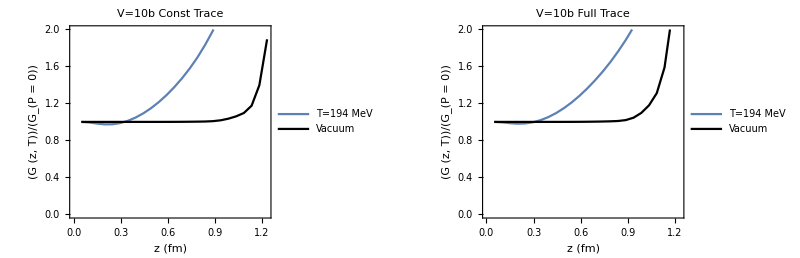

```mathematica
(*Plot of spatial correlation ratio verus its own P=0, vacuum is relative error+1*)
GraphicsRow[{ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialConstInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialConstInter["24.1"][[i,1,3,All,3,2]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])},{i,25}],Table[{SpatialNon["24.0"][[i,1,1]]hbarc,(Total[SpatialConstInter["24.0"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.0"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])/(Total[SpatialConstInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialConstInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Const Trace",PlotStyle->{Automatic,Black},PlotRange->{0,2},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","Vacuum"},LegendLayout->{"Column",2},LegendMarkerSize->10],{0.3,0.85}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"z (fm)","(G (z, T))/(G_(P = 0))"},FrameTicks->All,FrameStyle->Black],ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])},{i,25}],Table[{SpatialNon["24.0"][[i,1,1]]hbarc,(Total[SpatialTotalInter["24.0"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])/(Total[SpatialTotalInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Full Trace",PlotStyle->{Automatic,Black},PlotRange->{0,2},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","Vacuum"},LegendLayout->{"Column",2},LegendMarkerSize->10],{0.3,0.85}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"z (fm)","(G (z, T))/(G_(P = 0))"},FrameTicks->All,FrameStyle->Black]},ImageSize->800]
```

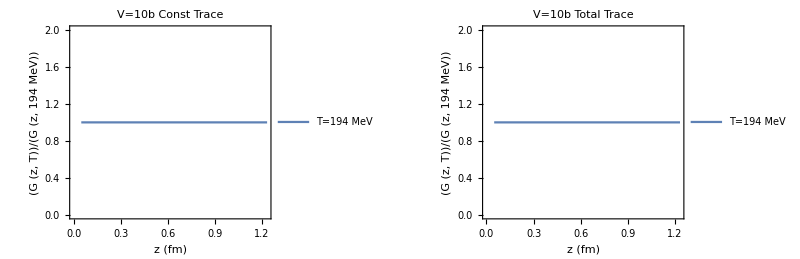

```mathematica
(*Plot of spatial correlation ratio normalized by coldest non-vacuum*)
GraphicsGrid[{{ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialConstInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialConstInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Const Trace",PlotRange->{0,2},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","Vacuum"},LegendLayout->{"Column",2}],{0.35,0.85}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"z (fm)","(G (z, T))/(G (z, 194 MeV))"},FrameTicks->All,FrameStyle->Black],ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Total Trace",PlotRange->{0,2},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","Vacuum"},LegendLayout->{"Column",2}],{0.35,0.85}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"z (fm)","(G (z, T))/(G (z, 194 MeV))"},FrameTicks->All,FrameStyle->Black]}},ImageSize->800]
```

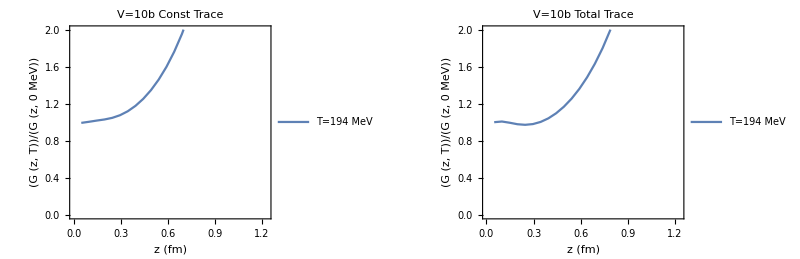

```mathematica
(*Plot of spatial correlation ratio normalized by vacuum*)
GraphicsGrid[{{ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialConstInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialConstInter["24.0"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.0"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Const Trace",PlotRange->{0,2},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","Vacuum"},LegendLayout->{"Column",2}],{0.35,0.85}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"z (fm)","(G (z, T))/(G (z, 0 MeV))"},FrameTicks->All,FrameStyle->Black],ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialTotalInter["24.0"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Total Trace",PlotRange->{0,2},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV","Vacuum"},LegendLayout->{"Column",2}],{0.35,0.85}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"z (fm)","(G (z, T))/(G (z, 0 MeV))"},FrameTicks->All,FrameStyle->Black]}},ImageSize->800]
```

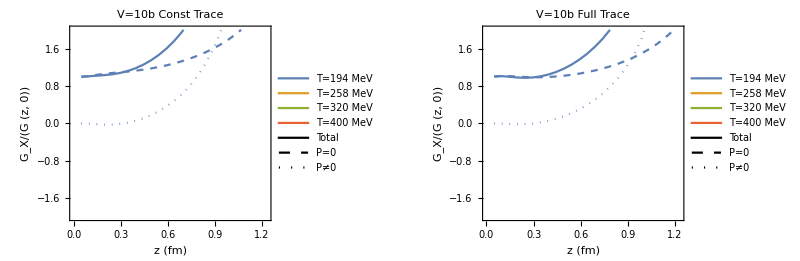

```mathematica
(*Plot of spatial correlation ratio contributions of P-dependence versus P=0 to vacuum normalized ratio*)
GraphicsRow[{Show[ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialConstInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialConstInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialConstInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Const Trace",PlotRange->{-2,2},LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,FrameStyle->Black],ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialConstInter["24.1"][[i,1,3,All,3,2]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialConstInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialConstInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Const Trace",PlotRange->{-2,2},LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,FrameStyle->Black,PlotStyle->Dashed],ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialConstInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]]-(Total[SpatialConstInter["24.1"][[i,1,3,All,3,2]]]+Total[SpatialConstInter["24.1"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]]))/(Total[SpatialConstInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialConstInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Const Trace",PlotRange->{-2,2},LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,FrameStyle->Black,PlotStyle->Dotted,PlotLegends->{Placed[LineLegend[Color,{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV"},LegendMarkerSize->10],{0.15,0.25}],Placed[LineLegend[{Black,{Black,Dashed},{Black,Dotted}},{"Total","P=0","P≠0"},LegendMarkerSize->15],{0.4,0.19}]}],FrameLabel->{"z (fm)","G_X/(G (z, 0))"}],Show[ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialTotalInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Full Trace",PlotRange->{-2,2},LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,FrameStyle->Black],ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialTotalInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Full Trace",PlotRange->{-2,2},LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,FrameStyle->Black,PlotStyle->Dashed],ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]]-(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]]))/(Total[SpatialTotalInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Full Trace",PlotRange->{-2,2},LabelStyle->Black,ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,FrameStyle->Black,PlotStyle->Dotted,PlotLegends->{Placed[LineLegend[Color,{"T=194 MeV","T=258 MeV","T=320 MeV","T=400 MeV"},LegendMarkerSize->10],{0.15,0.25}],Placed[LineLegend[{Black,{Black,Dashed},{Black,Dotted}},{"Total","P=0","P≠0"},LegendMarkerSize->15],{0.4,0.19}]}],FrameLabel->{"z (fm)","G_X/(G (z, 0))"}]},ImageSize->800]
```

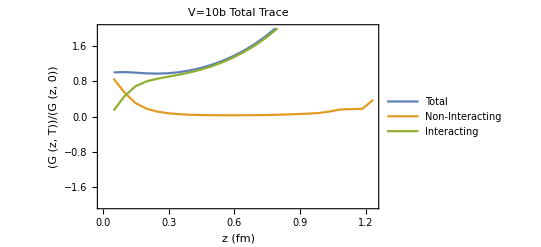

```mathematica
(*Plot of spatial correlation ratio contributions of interacting versus non-interacting to vacuum normalized ratio*)
ListPlot[{Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,1]]]+Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialTotalInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}],Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[Select[SpatialNon["24.1"][[i,1,3]],#[[1]]<49&][[All,3,1]]]+Total[SpatialNon["24.1"][[i,1,4,-29;;-2,3,1]]]+Total[SpatialNon["24.1"][[i,1,5,29,2]]])/(Total[SpatialTotalInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}],Table[{SpatialNon["24.1"][[i,1,1]]hbarc,(Total[SpatialTotalInter["24.1"][[i,1,3,All,3,1]]]+Total[SpatialTotalInter["24.1"][[i,1,4,-29;;,3,1]]])/(Total[SpatialTotalInter["24.0"][[i,1,3,All,3,2]]]+Total[SpatialTotalInter["24.0"][[i,1,4,-29;;,3,2]]]+Total[Select[SpatialNon["24.0"][[i,1,3]],#[[1]]<49&][[All,3,2]]]+Total[SpatialNon["24.0"][[i,1,4,-29;;-2,3,2]]]+Total[SpatialNon["24.0"][[i,1,5,29,2]]])},{i,25}]},Joined->True,PlotLabel->"V=10b Total Trace",PlotRange->{-2,2},LabelStyle->Black,PlotLegends->Placed[LineLegend[{"Total","Non-Interacting","Interacting"},LegendLayout->{"Column",2}],{0.35,0.15}],ImageSize->400,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"z (fm)","(G (z, T))/(G (z, 0))"},FrameTicks->All,FrameStyle->Black]
```

```mathematica
Speak["Full Width Mathematica Done"]
```